```mathematica
rawdata=Import["~/montecarloPi/data.csv"];data=Table[{rawdata[[i,3]],rawdata[[i,2]]},{j,1,4},{i,j,Length[rawdata],4}];
fits=Table[Normal[LinearModelFit[data[[i]],x,x]],{i,1,Length[data]}];
```

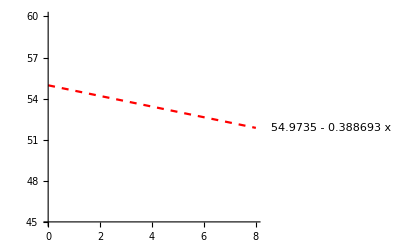

```mathematica
linearfit=Plot[Total[fits]/Length[fits],{x,0,8},PlotRange->{45,60},PlotStyle->{Red,Dashed},PlotLabels->{ToString[Simplify[Total[fits]/Length[fits]]]}]
```

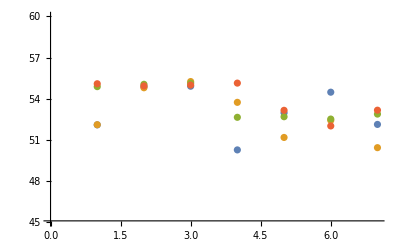

```mathematica
points=ListPlot[data,PlotRange->{45,60}]
```

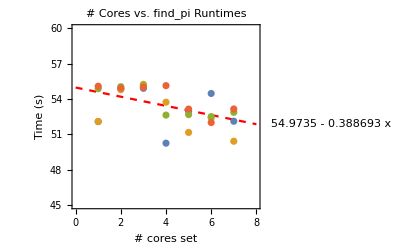

```mathematica
final=Show[{linearfit,points},Frame->True,FrameLabel->{"# cores set","Time (s)"},LabelStyle->Bold,PlotLabel->"# Cores vs. find_pi Runtimes"]
```

```mathematica
Rasterize[final,ImageResolution->250]
```

-Graphics-